```mathematica
res=Integrate[Sqrt[y]E^(-(x^2 y^2+a^2 z y)/(2a^2 x^2 d^2)),{y,0,Infinity},Assumptions->{a>0,x>0,d>0,z>0}]
```

-1/(8 √2 x^3 √z)a ⅇ^((a^2 z^2)/(16 d^2 x^4)) π (a^2 z^2 BesselI[-1/4,(a^2 z^2)/(16 d^2 x^4)]-(8 d^2 x^4+a^2 z^2) BesselI[1/4,(a^2 z^2)/(16 d^2 x^4)]+a^2 z^2 (BesselI[3/4,(a^2 z^2)/(16 d^2 x^4)]-BesselI[5/4,(a^2 z^2)/(16 d^2 x^4)]))

```mathematica
FullSimplify[res/Sqrt[z]]
```

-(a^3 ⅇ^((a^2 z^2)/(16 d^2 x^4)) z (BesselK[1/4,(a^2 z^2)/(16 d^2 x^4)]-BesselK[3/4,(a^2 z^2)/(16 d^2 x^4)]))/(8 x^3)

```mathematica
res2=Integrate[Sqrt[y]E^(-(x^2 y^2+a^2 z y)/(b)),{y,0,Infinity},Assumptions->{a>0,x>0,d>0,z>0,b>0}]
```

-(a^3 ⅇ^((a^4 z^2)/(8 b x^2)) z^(3/2) (BesselK[1/4,(a^4 z^2)/(8 b x^2)]-BesselK[3/4,(a^4 z^2)/(8 b x^2)]))/(8 x^3)

```mathematica
FullSimplify[res2]
```

-(a^3 ⅇ^((a^4 z^2)/(8 b x^2)) z^(3/2) (BesselK[1/4,(a^4 z^2)/(8 b x^2)]-BesselK[3/4,(a^4 z^2)/(8 b x^2)]))/(8 x^3)

```mathematica
TeXForm[FullSimplify[res]]
```

-\frac{a^3 z^{3/2} e^{\frac{a^2 z^2}{16 d^2 x^4}}
   \left(K_{\frac{1}{4}}\left(\frac{a^2 z^2}{16 d^2
   x^4}\right)-K_{\frac{3}{4}}\left(\frac{a^2 z^2}{16 d^2
   x^4}\right)\right)}{8 x^3}

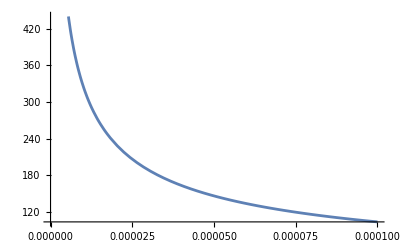

```mathematica
Plot[res/Sqrt[z]/.{a->1,x->1,d->1},{z,0,0.0001}]
```

```mathematica
Limit[res/.{a->1,x->1,d->1},z->0]
```

Indeterminate